# Gossip Algorithms over different network topologies

A brief description of three different gossip algorithms, Probabilistic Broadcast, Probabilistic Edge, Fixed Fanout, with detailed example on how do they work over different network topologies, Erdős–Rényi, Random Geometric Graph, scale free.

## Random Graph

Gossip algorithms are a system of machine-to-machine communication whose goal is to minimize the channel usage and maximise the coverage of the network. Network can be seen as graph of nodes witch node represent a computer and edge represent connection.

Example of a random graph:

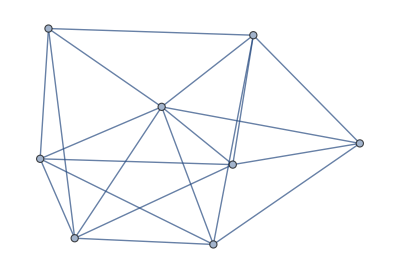

```mathematica
randomGraph=RandomGraph[{8,20}]
```

A pure mechanism of broadcast send the message to all the other node connected with the source, this method leads to a complete coverage of the message in the graph but on the other hand cause the saturation of the channel.

In red the source of the message, mail on edge involved

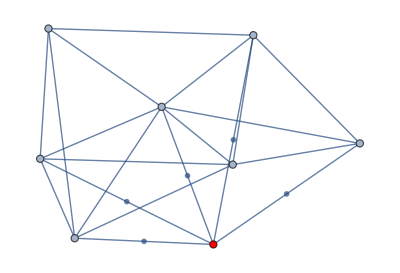

```mathematica
SetProperty[{SetProperty[{randomGraph, EdgeList[randomGraph,1<->_ ]}, EdgeLabels -> -Graphics-],1},VertexStyle->Red]
```

## Symbols and Functions

There are three most famous gossip algorithm, their difference is mostly related on how do they choose the node to whom forward the message. They are named in literature Probabilistic Broadcast (PB), Probabilistic Edge (PE) e Fixed Fanout (FF).
In order to better understand the algorithm it’s important to introduce some notation

Λ = set of node adjacent to node i

1→{2,3,4,6,8}

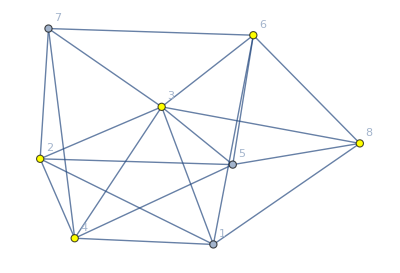

```mathematica
Λ[graph_,i_]:=Map[Last,EdgeList[graph,i<->_ ]]
1->Λ[randomGraph,1]
SetProperty[{SetProperty[randomGraph,VertexLabels->"Name"],Λ[randomGraph,1]},VertexStyle->Yellow]
```

V = cardinality of Λ_i

```mathematica
V[graph_,i_]:=Length[Λ[graph,i]]
V[randomGraph,1]
```

5

msg = the message received
p_v , p_e , fanout = probabilistic value related with the algorithm, PB,PE,EF.

## Probabilistic Broadcast

The first algorithm is Probabilistic Broadcast, the value p_v is the threshold that decide if the message will be send in broadcast or dropped from the node i .

example of Probabilistic Broadcast with p_v= 0.3

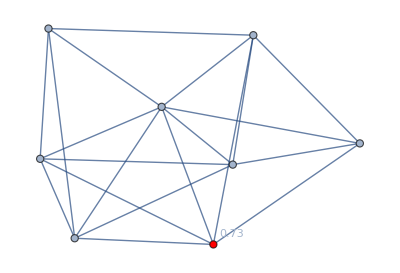
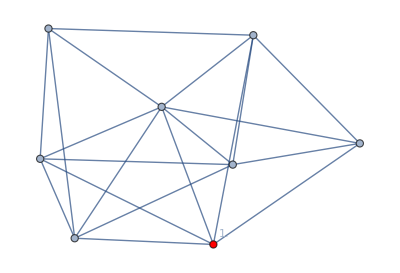
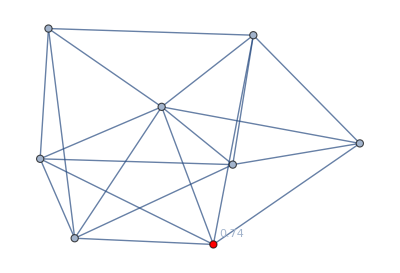
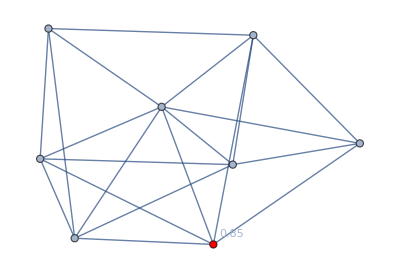
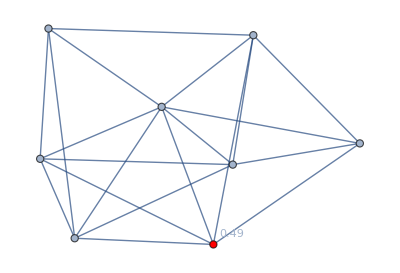
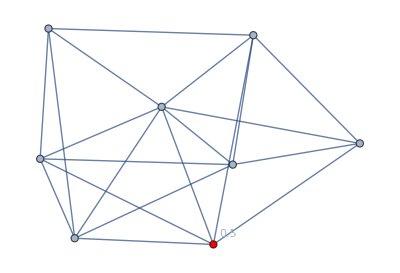
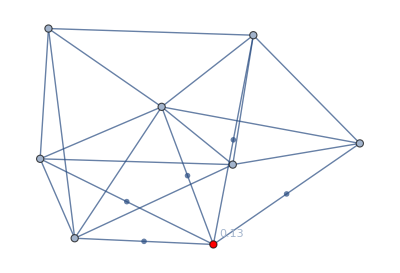
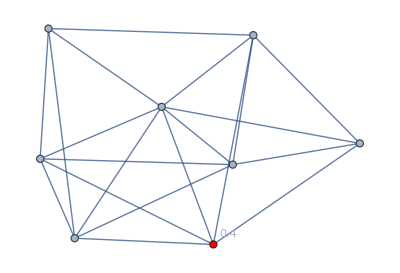

```mathematica
ProbabilisticBroadcast[graph_,i_,msg_,pv_]:= With[
{r=RandomReal[]},If[
r≤ pv,
SetProperty[{SetProperty[{SetProperty[{graph, EdgeList[graph,i<->_ ]}, EdgeLabels -> msg],i},VertexStyle->Red],i},VertexLabels->{SetPrecision[r,2]}],
SetProperty[{SetProperty[{graph,i},VertexStyle->Red],i},VertexLabels->{SetPrecision[r,2]}]
]]
Table[ProbabilisticBroadcast[randomGraph,1,-Graphics-,.3],{x,1,10}]
```

## Probabilistic Edge

The second algorithm is Probabilistic Edge, the value p_e is the threshold that decide if the message will be send on a specific edge or not from the node i.

example of edge selection with Probabilistic Edge with p_e= 0.3

```mathematica
GetEdge[graph_,i_,pe_]:=Map[First,Select[Map[With[{r=RandomReal[]≤pe},{#,r}]&,Map[i->#&,Λ[graph,1]]],Last[#]==True&]]
GetEdge[randomGraph,1,.3]
```

{1→4}

example Probabilistic Edge with p_e= 0.4

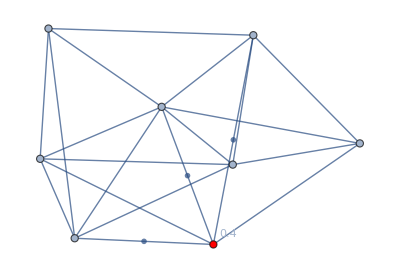
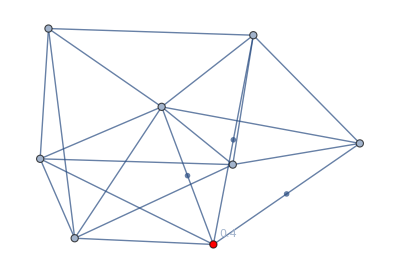
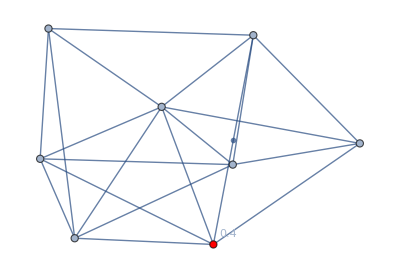
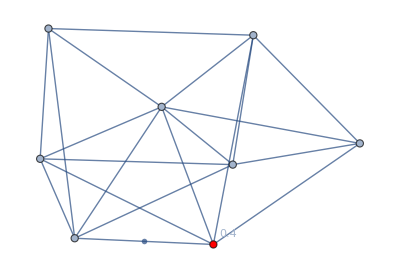
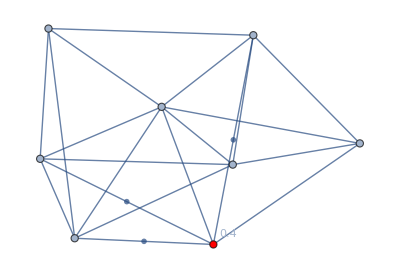
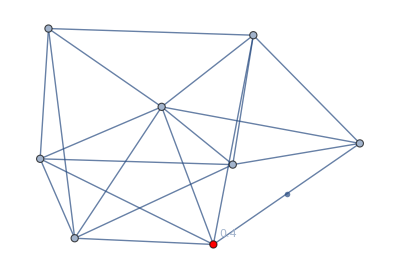
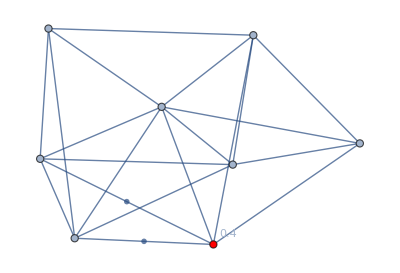
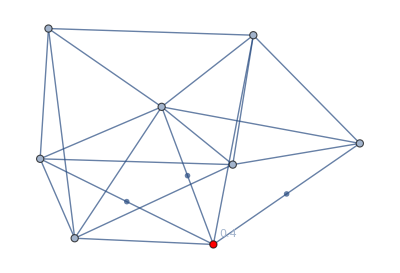
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[ProbabilisticEdge]
ProbabilisticEdge[graph_,i_,msg_,pe_]:=
SetProperty[{SetProperty[{SetProperty[{graph, GetEdge[graph,i,pe ]}, EdgeLabels -> msg],i},VertexStyle->Red],i},VertexLabels->{SetPrecision[pe,2]}]
Table[ProbabilisticEdge[randomGraph,1,-Graphics-,.4],{x,1,10}]
```

It’s expected a number of message  ~ V_1 * n°Example * p_e

```mathematica
V[randomGraph,1]*10*.4
```

20.

## Fixed Fanout

The last algorithm is Fixed Fanout the node choose a number of random node connected with him to whom send the message.

example of fanout selection with Fixed Fanout with 0<= fanout <= V_i

```mathematica
Clear[GetEdgeFanout]
GetEdgeFanout[graph_,i_,fanout_]:=RandomSample[Map[i->#&,Λ[graph,1]],fanout]
GetEdgeFanout[randomGraph,1,RandomInteger[{0,V[randomGraph,1]}]]
```

{1→3,1→4}

example Fixed Fanout with  0<= fanout <= V_i

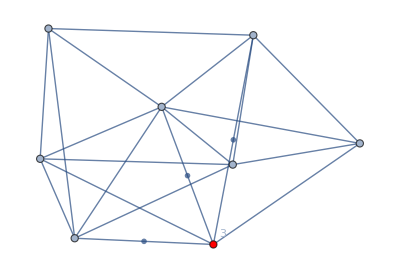
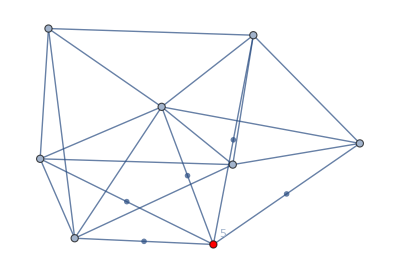
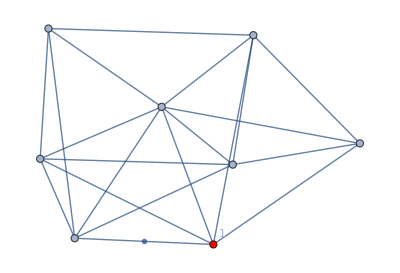
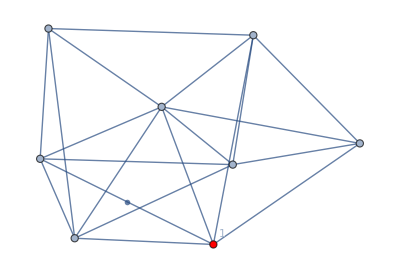
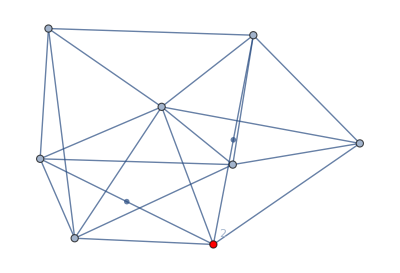
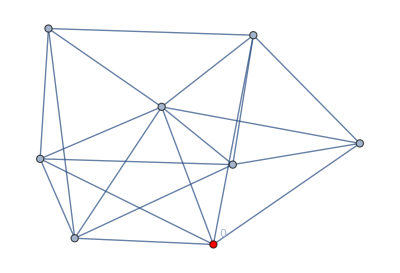
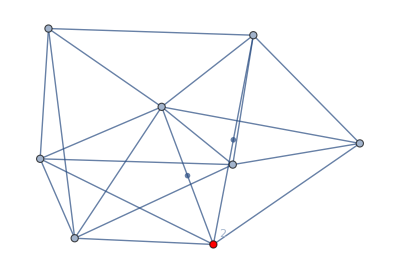
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[FixedFanout]
FixedFanout[graph_,i_,msg_,fanout_]:=SetProperty[{SetProperty[{SetProperty[{graph, GetEdgeFanout[graph,i,fanout]}, EdgeLabels -> msg],i},VertexStyle->Red],i},VertexLabels->{fanout}]
Table[FixedFanout[randomGraph,1,-Graphics-,RandomInteger[{0,V[randomGraph,1]}]],{x,1,10}]
```

## Erdős–Rényi or Bernulli graph

There are an infinity number of graph topology here are shown only the ones more important for this case study.
Erdős–Rényi graph also called Bernulli graph is one of the most important way to generate RandomGraph.
A Bernoulli graph distribution leads to graph with n-vertex and an edge probability p.

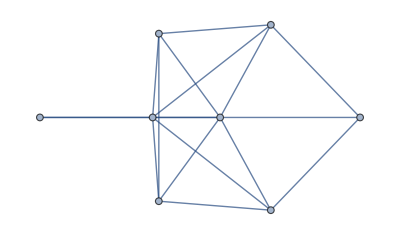

```mathematica
RandomGraph[BernoulliGraphDistribution[8,.6]]
```

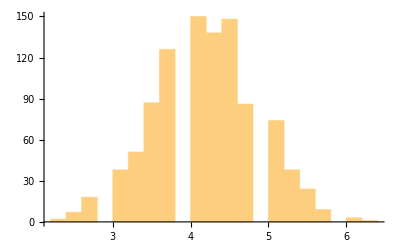

```mathematica
meanVertexDegree=Mean /@VertexDegree /@ RandomGraph[BernoulliGraphDistribution[8,0.6],10^3];
Show[Histogram[meanVertexDegree,Automatic]]
```

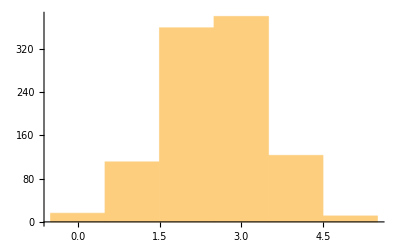

```mathematica
edgeConnectivity=EdgeConnectivity /@ RandomGraph[BernoulliGraphDistribution[8,0.6],10^3];
Show[Histogram[edgeConnectivity,Automatic]]
```

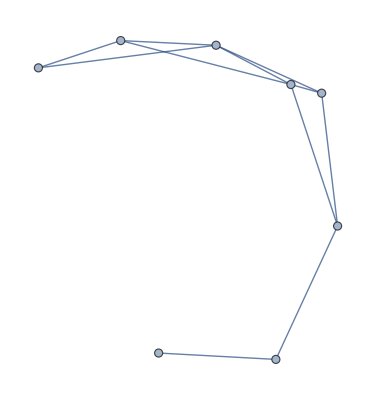

```mathematica
RandomGraph[SpatialGraphDistribution[8,.6]]
```

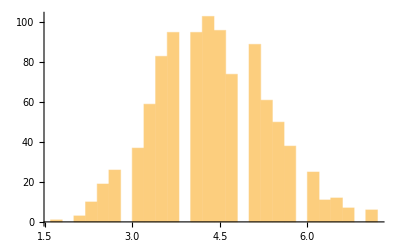

```mathematica
meanVertexDegreeSG=Mean /@VertexDegree /@ RandomGraph[SpatialGraphDistribution[8,0.6],10^3];
Show[Histogram[meanVertexDegreeSG,Automatic]]
```

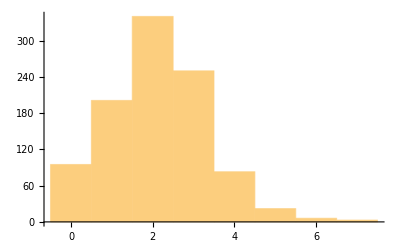

```mathematica
edgeConnectivitySG=EdgeConnectivity /@ RandomGraph[SpatialGraphDistribution[8,0.6],10^3];
Show[Histogram[edgeConnectivitySG,Automatic]]
```

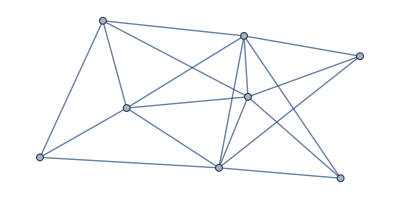

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[30,5]]
```

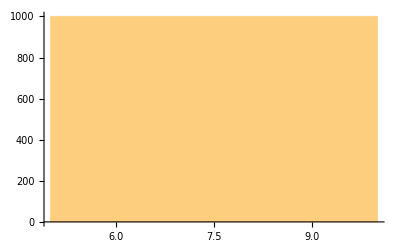

```mathematica
meanVertexDegreeSF=Mean /@VertexDegree /@ RandomGraph[BarabasiAlbertGraphDistribution[30,5],10^3];
Show[Histogram[meanVertexDegreeSF,Automatic]]
```

```mathematica
EdgeConnectivity[RandomGraph[BarabasiAlbertGraphDistribution[30,3]]]
edgeConnectivitySF=EdgeConnectivity /@ RandomGraph[BarabasiAlbertGraphDistribution[30,5],10^3];
Show[Histogram[edgeConnectivitySF,Automatic]]
```

3

-Graphics-

```mathematica
{Show[Histogram[meanVertexDegree,Automatic]],Show[Histogram[meanVertexDegreeSG,Automatic]],Show[Histogram[meanVertexDegreeSF,Automatic]]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Show[Histogram[edgeConnectivity,Automatic]],Show[Histogram[edgeConnectivitySG,Automatic]],Show[Histogram[edgeConnectivitySF,Automatic]]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Add more sections as needed to explain the topic (cmd/alt+4)

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Daniele Baschieri

20/06/2017

daniele.baschieri@gmail.com